Inserisco la matrice A

```mathematica
A=({{3/8, -1/16, -1/16}, {-5/6, 1/12, 5/12}, {7/12, 7/24, -1/24}})
```

{{3/8,-1/16,-1/16},{-5/6,1/12,5/12},{7/12,7/24,-1/24}}

Calcolo gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{1/2,-1/3,1/4}

Mi calcolo la matrice degli autovettori dx di A

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{-1/2,0,1/2},{1,-1,0},{0,1,1}}

```mathematica
MatrixForm[T]
```

(-1/2 | 0 | 1/2
1 | -1 | 0
0 | 1 | 1)

```mathematica
λ
```

{1/2,-1/3,1/4}

Calcolo la forma diagonale di A

```mathematica
Inverse[T].A.T
```

{{1/2,0,0},{0,-1/3,0},{0,0,1/4}}

```mathematica
MatrixForm[Inverse[T].A.T]
```

(1/2 | 0 | 0
0 | -1/3 | 0
0 | 0 | 1/4)

Calcolo la risposta libera, inizio definendo lo stato iniziale

```mathematica
x0=({{-1}, {2}, {3}})
```

{{-1},{2},{3}}

Proietto lo stato iniziale nella base di R^3 individuata dalle colonne di T

```mathematica
z0=Inverse[T].x0
```

{{7/2},{3/2},{3/2}}

```mathematica
MatrixForm[z0]
```

(7/2
3/2
3/2)

```mathematica
z0[[1,1]]
```

7/2

```mathematica
xl[k_]:=∑_(i=1)^3 T[[All,i]](λ[[i]])^k z0[[i,1]]
```

```mathematica
xl[k]
```

{-7 2^(-2-k)+3 4^(-1-k),7 2^(-1-k)-1/2 (-1)^k 3^(1-k),3 2^(-1-2 k)+1/2 (-1)^k 3^(1-k)}

Grafico in forma di successione delle componenti della risposta libera

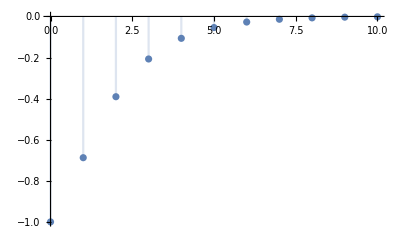

```mathematica
DiscretePlot[xl[k][[1]],{k,0,10}]
```

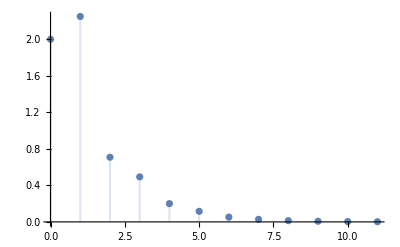

```mathematica
DiscretePlot[xl[k][[2]],{k,0,11}]
```

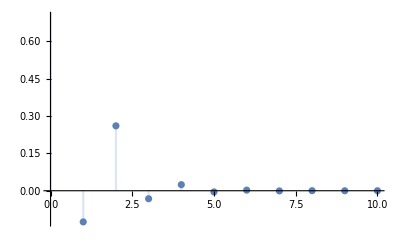

```mathematica
DiscretePlot[xl[k][[3]],{k,0,10}]
```